# Bound Reference (By me :)

### READ ME!!!

This bound reference is intended to be used with the Tools.wls package. If you’re not using it, please don’t use this, as it will be missing pretty important information.

I highly recommend either a) Use the package while using your own bound reference (documentation on the functions of the package will be available)
				        or b) You use the package and modify this reference to suit you
				    
Please don’t use the package and this bound reference blindly. If it is the day before a SAC or god forbid the exams, use what you know, instead of relying on my god-forsaken code.

(Also if my code results in you losing some marks, I’m honestly really sorry and I’ll do my best to fix it what made that happen, but I’m providing this resource out of my free time so don’t use this without accepting that my code might be shit)

### Installation of Package

Install the package onto this link:	

Make sure that the package, and the notebook you’re working with are in the same directory.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\mathematica\notes

```mathematica
<< Tools.wl
```

To make sure that this has actually succeeded, check for the definition of a command like:

## Topic 2: Inverse Functions & Relations

#### Inverse of a Function With Restricted Domain (For purposes of creating an inverse)

```mathematica
ClearAll[h]
```

```mathematica
(*Function Must be defined this way in order for inverse to work*)
h:=Function[x,ConditionalExpression[(x-4)^2+2,x<= 4]]
```

```mathematica
h[x]
```

ConditionalExpression[2+(-4+x)^2, x≤4]

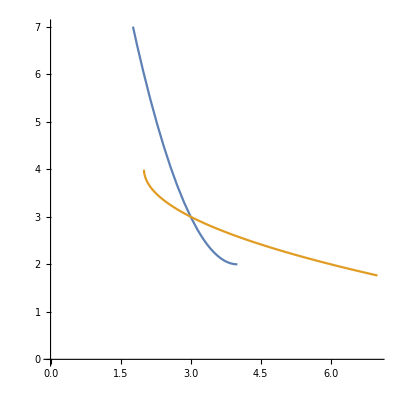

```mathematica
Plot[{h[x],InverseFunction[h][x]},{x,0,7},AspectRatio->1,PlotRange->{0,7}]
```

## Topic 3: Families of Functions

### Finding Rules of Hyperbola

The points (2, 1) and (10, 6) lie on the curve with the equation y=a/(n x+4)-3.  Find a and n and hence state the full equation in the form y=-a/(n x+c)-3, where a, n and c are integers.

```mathematica
f[x_]:=-a/(n x+4)-3
```

```mathematica
Solve[f[2]==1&&f[10]==6,{a,n}]
```

{{a→-576/41,n→-10/41}}

```mathematica
(*Substitute values into original equation*)
(-a/(n x + 4)/.{a->-576/41,n->-10/41}//Simplify)-3
```

-3+288/(82-5 x)

### Matrix Transformation

The transformation is defined as:
[X
Y]=[3 | 0
0 | 2].[x
y]+[-1
4]
Find the image of y = 2 x^2+1 under this transformation in terms of 
ax^2+bx+c:

```mathematica
(* Find x and y in terms of x' and y'*)
Solve[({{X}, {Y}})==({{3, 0}, {0, 2}}).({{x}, {y}})+({{-1}, {4}}),{x,y}]
```

{{x→(1+X)/3,y→1/2 (-4+Y)}}

```mathematica
(* Substitue values into original equation and rearrange in terms of Y*)
Solve[2 x^2+1==y/.{x->(1+X)/3,y->1/2 (-4+Y)},Y]//Expand
```

{{Y→58/9+(8 X)/9+(4 X^2)/9}}

```mathematica
f[1]
```

9

```mathematica
ClearAll[f]
```

```mathematica
f:=ConditionalFunction[x,x+1,x>2]
```

```mathematica
f[x]
```

ConditionalExpression[1+x, x>2]

```mathematica
Plot[{f[x]},{x,-5,5}]
```

Function::flpar: Parameter specification -4.9998 in Function[-4.9998,-] should be a symbol or a list of symbols.

Function::flpar: Parameter specification -4.79571 in Function[-4.79571,-] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

-Graphics-